## Bounds on EDGB Theory From the Overall Posterior of GW151226

```mathematica
ClearAll
```

ClearAll

```mathematica
dataOverall1=Import[NotebookDirectory[]<>"/overall_post.csv","CSV"] (*Posterior containing cos_theta_inc,luminosity distance,right ascension, declination, m1_det,m2_det,spin_1,spin_2,cos_tilt1,cos_tilt2 respectively.*)
```

{{0.273997,245.073,3.58022,-0.392013,15.7931,8.16902,0.474815,0.0924668,0.861707,-0.349195},52250,{0.795965,311.364,3.41712,-0.0397626,13.4479,9.18584,0.303922,0.287212,0.401218,0.583816}}
 |  |  |  |

```mathematica
dataOverall2=Import[NotebookDirectory[]<>"/-1pn-all-beta.csv","CSV"] ; (*PPE beta*)
dataOverall3=Import[NotebookDirectory[]<>"/-1pn-all-alpha.csv","CSV"] ;(*PPE alpha*)
```

```mathematica
χ1All=dataOverall1[[All,7]]; (*Dimensionles spin parameter*)
χ2All=dataOverall1[[All,8]];
```

We want to write redshift z in terms of luminosity distance DL following Eq. 2.16 of 0411129, since LIGO data gives us DL

```mathematica
DL=dataOverall1[[All,2]]*10^6*3.261636*tyear/.tyear->3.1536*10^7
```

{2.52079×10^16,4.85528×10^16,6.35231×10^16,5.24927×10^16,3.73515×10^16,3.05455×10^16,4.78442×10^16,52238,3.80794×10^16,5.61282×10^16,5.43259×10^16,5.42488×10^16,3.54656×10^16,4.06701×10^16,3.20266×10^16}
 |  |  |  |

```mathematica
Clear[z]
```

```mathematica
Clear[z1,z2]
```

```mathematica
$Assumptions:=z1<1
```

```mathematica
A=Series[(ωM(1+z1)^3+ωΛ)^(-1/2),{z1,0,1}]//Normal
```

-(3 z1 ωM)/(2 (ωM+ωΛ)^(3/2))+1/(√(ωM+ωΛ))

```mathematica
B=(1+z)/H0 Integrate[A,{z1,0,z}]//Expand
```

-(3 z^2 ωM)/(4 H0 (ωM+ωΛ)^(3/2))-(3 z^3 ωM)/(4 H0 (ωM+ωΛ)^(3/2))+z/(H0 √(ωM+ωΛ))+z^2/(H0 √(ωM+ωΛ))

```mathematica
B2=Series[B,{z,0,2}]//Normal
```

z/(H0 √(ωM+ωΛ))+(z^2 (ωM+4 ωΛ))/(4 H0 (ωM+ωΛ)^(3/2))

```mathematica
Clear[z]
```

```mathematica
z=z/.Solve[B2-Dl==0,z][[2]]
```

(2 H0 (ωM+ωΛ)^(3/2) (-1/(H0 √(ωM+ωΛ))+√(1/(H0^2 (ωM+ωΛ))+(Dl (ωM+4 ωΛ))/(H0 (ωM+ωΛ)^(3/2)))))/(ωM+4 ωΛ)

```mathematica
z2=z/.{Dl->DL,ωM->0.3111,ωΛ->0.6889,α->0,H0->2.2683085*10^-18}
```

{0.054871,0.102135,0.130944,0.109823,0.0798379,0.0659518,0.100744,0.0844401,52237,0.0813074,0.116848,0.113374,0.113224,0.0760166,0.086514,0.0689964}
 |  |  |  |

```mathematica
m1All=dataOverall1[[All,5]]/(1+z2)*tsolar/.tsolar->4.925491*10^-6 (*Ligo posterior gives mass in detector frame*);
m2All=dataOverall1[[All,6]]/(1+z2)*tsolar/.tsolar->4.925491*10^-6;
```

```mathematica
ηAll=(m1All*m2All)/(m1All+m2All)^2;
```

```mathematica
βppEAll=1/1.64485*dataOverall2[[All,1]];(*1-sigma upper bound*)
αppEAll=1/1.64485*dataOverall3[[All,1]](*1-sigma upper bound*);
```

```mathematica
s1All=2/χ1All^2*(√(1-χ1All^2)-1+χ1All^2);
s2All=2/χ2All^2*(√(1-χ2All^2)-1+χ2All^2);
```

```mathematica
ζphaseAll=Abs[-7168/5*((m1All+m2All)^4*ηAll^(18/5))/(((m1All^2*s2All)-(m2All^2*s1All))^2)*βppEAll] ;(*Sigma_Zeta from phase corrections.Eqn. 29 of 1809.00259*);
```

```mathematica
ζampAll=Abs[-192/5*((m1All+m2All)^4*ηAll^(18/5))/(((m1All^2*s2All)-(m2All^2*s1All))^2)*αppEAll]; (*Sigma_Zeta from amplitude corrections*)
```

```mathematica
Length[m1All]
```

52252

```mathematica
Length[βppEAll]
```

52252

```mathematica
Mean[ζampAll]
```

12509.6

```mathematica
Mean[ζphaseAll]
```

360.999

```mathematica
ζAllphaseSelected=Select[ζphaseAll,# <1 &]; (*Datasets that satisfy Zeta<1 where Zeta is found from phase correction. Since the distribution of zeta is Gaussian with zero mean, sigma_zeta<1 and zeta<1 are analogous*)
ζAllampSelected=Select[ζampAll,# <1 &];(*Datasets that satisfy Zeta<1 where Zeta is found from amplitude correction*)
```

```mathematica
Length[ζAllphaseSelected]
```

51355

```mathematica
Length[ζAllampSelected]
```

46872

```mathematica
Mean[ζAllphaseSelected]
```

0.0174016

```mathematica
StandardDeviation[ζAllphaseSelected]
```

0.074786

```mathematica
A1=Table[Append[dataOverall1[[i]],ζphaseAll[[i]]],{i,1,Length[dataOverall1]}]
```

{{0.273997,245.073,3.58022,-0.392013,15.7931,8.16902,0.474815,0.0924668,0.861707,-0.349195,0.000527219},52250,{0.795965,311.364,3.41712,-0.0397626,13.4479,9.18584,0.303922,0.287212,0.401218,0.583816,0.00193851}}
 |  |  |  |

```mathematica
A2=Table[Append[A1[[i]],ζampAll[[i]]],{i,1,Length[A1]}] (*Contains all the posterior data and sigma_zeta from both phase and amplitude corrections*)
```

{{0.273997,245.073,3.58022,-0.392013,15.7931,8.16902,0.474815,0.0924668,0.861707,-0.349195,0.000527219,0.0171763},52250,{0.795965,311.364,3.41712,-0.0397626,4,0.401218,0.583816,0.00193851,0.0686092}}
 |  |  |  |

```mathematica
A3=Select[A2,#[[11]]<1&][[All,{1,2,3,4,5,6,7,8,9,10}]] (*Data satisfying zeta_phase<1*)
```

{{0.273997,245.073,3.58022,-0.392013,15.7931,8.16902,0.474815,0.0924668,0.861707,-0.349195},51353,{0.795965,311.364,3.41712,-0.0397626,13.4479,9.18584,0.303922,0.287212,0.401218,0.583816}}
 |  |  |  |

```mathematica
A4=Select[A2,#[[12]]<1&][[All,{1,2,3,4,5,6,7,8,9,10,11,12}]](*Data satisfying zeta_amp<1*)
```

{{0.273997,245.073,3.58022,-0.392013,15.7931,8.16902,0.474815,0.0924668,0.861707,-0.349195,0.000527219,0.0171763},46870,{0.795965,311.364,3.41712,-0.0397626,4,0.401218,0.583816,0.00193851,0.0686092}}
 |  |  |  |

```mathematica
A4[[All,12]]
```

{0.0171763,0.0522075,0.165549,0.0378357,0.0127864,0.0533918,0.0167203,0.0161527,46857,0.0140803,0.0231292,0.000514475,0.0374042,0.727602,0.0315771,0.0686092}
 |  |  |  |

```mathematica
Length[A3]
```

51355

```mathematica
Length[A4]
```

46872

```mathematica
Select[A4[[All,11]],#>1&]  (*Proves that all 46872 data with zeta_amp<1 also satisfies zeta_phase<1*)
```

{}

```mathematica
Mean[ζAllampSelected]
```

0.094265

```mathematica
SqrtαEDGBamp=((ζampAll*(m1All+m2All)^4)/(16*π))^(1/4)*3*10^5(*square root of alpha_EDGB (in km) from the amplitdue corrections of all data*)
SqrtαEDGBphase=((ζphaseAll*(m1All+m2All)^4)/(16*π))^(1/4)*3*10^5(*square root of alpha_EDGB from the phase corrections of all data*)
```

{4.56364,12.6105,5.4262,7.22392,11.6606,5.28992,4.09261,6.1827,52236,4.45133,4.76263,4.70977,2.48538,5.09212,10.6284,4.99241,6.01353}
 |  |  |  |

{1.91019,5.21213,2.2308,2.9689,4.80666,2.17614,1.73487,2.71404,52236,1.85657,2.1935,2.03295,1.19177,2.12762,4.37913,2.05849,2.46547}
 |  |  |  |

```mathematica
Mean[SqrtαEDGBamp] (*just a rough estimate for sanity check. This does not give a statistically meaningful bound*)
```

7.19566

```mathematica
Mean[SqrtαEDGBphase]
```

3.02733

```mathematica
tsolar=4.925491*10^-6
```

4.92549×10^-6

```mathematica
SqrtαEDGBphaseSelected=((A4[[All,11]]*(A4[[All,5]]*tsolar+A4[[All,6]]*tsolar)^4)/(16*π))^(1/4)*3*10^5 (*square root of alpha_EDGB from phase correction of the data satisfying zeta_phase<1*)
```

{2.015,2.52291,3.29495,2.31966,1.90965,2.94321,2.04561,1.98368,46856,2.05282,2.37185,2.2705,1.32689,2.36852,4.71202,2.23658,2.63558}
 |  |  |  |

```mathematica
SqrtαEDGBampSelected=((A4[[All,12]]*(A4[[All,5]]*tsolar+A4[[All,6]]*tsolar)^4)/(16*π))^(1/4)*3*10^5 (*square root of alpha from amplitude correction of the data satisfying zeta_amp<1*)
```

{4.81405,6.13673,8.01727,5.6388,4.50492,6.70477,4.82258,4.70667,46856,4.92185,5.14987,5.2601,2.76716,5.66867,11.4363,5.42432,6.42844}
 |  |  |  |

```mathematica
Mean[SqrtαEDGBphaseSelected]
```

2.47235

```mathematica
Mean[SqrtαEDGBampSelected]
```

5.82508

(α^2)_EDGB from phase correction:

```mathematica
LogSquaredαPhase=Log[SqrtαEDGBphase^4] (*This is Log of sigma_(alpha^2)*)
```

{2.58881,6.60395,3.20944,4.35276,6.28001,3.11021,2.20374,3.99375,52236,2.47493,3.14199,2.83796,0.701765,3.02001,5.9074,2.88789,3.60954}
 |  |  |  |

```mathematica
Max[LogSquaredαPhase]
```

25.6805

```mathematica
Min[LogSquaredαPhase]
```

-0.47451

```mathematica
𝒟logα=HistogramDistribution[LogSquaredαPhase] ;
```

```mathematica
pslogαPhase=PDF[𝒟logα,x];
```

```mathematica
Histogram[LogSquaredαPhase];
```

```mathematica
fun1αphase[x_,y_]=1/(√(2*π)*Exp[y])*Exp[-x^2/(2Exp[2*y])] (*P(α^2|Subscript[σ, α^2])*)
```

(ⅇ^(-1/2 ⅇ^(-2 y) x^2-y))/(√(2 π))

```mathematica
αSampleLog=Prepend[10^Range[-6,11,0.1],0];(*Sample Subscript[σ, α^2] for integration. I decided to include 0 in the sample*)
```

```mathematica
fun1αphaseTable[y_]=Table[{αSampleLog[[i]],fun1αphase[αSampleLog[[i]],y]},{i,1,Length[αSampleLog]}]; (*Table for fun1αphase*)
```

```mathematica
αPhaseMC[x_]=pslogαPhase;
```

```mathematica
αPhaseMC[-0.25]
```

0.00218173

```mathematica
αPhaseMC[27]
```

0.

```mathematica
αMCSample=Range[-0.25,27,0.5];
```

```mathematica
αMCTable=Table[{αMCSample[[i]],αPhaseMC[αMCSample[[i]]]},{i,1,Length[αMCSample]}];
```

```mathematica
αMCTableInterp=Interpolation[αMCTable];
```

```mathematica
plotαMCTableInterp=Plot[αMCTableInterp[x],{x,-0.25,27},PlotStyle->Blue,PlotLegends->{"Interpolation"},PlotRange->All];
```

```mathematica
plot5=Plot[αPhaseMC[x],{x,-0.25,27},Filling->Axis,PlotStyle->Gray,PlotRange->All];
```

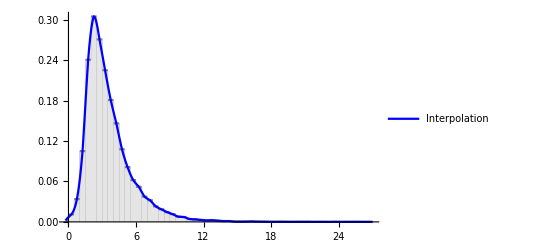

```mathematica
Show[plot5,plotαMCTableInterp] (*Interpolation matches the actual pdf of monte-carlo*)
```

```mathematica
αFinalPDFPhaseLog=Table[{fun1αphaseTable[y][[i,1]],NIntegrate[fun1αphaseTable[y][[i,2]]αMCTableInterp[y],{y,-0.25,27}]},{i,1,Length[fun1αphaseTable[y]]}];
```

```mathematica
αFinalPDFPhaseInterpLog=Interpolation[αFinalPDFPhaseLog];
```

```mathematica
αNormalization=NIntegrate[αFinalPDFPhaseInterpLog[x],{x,0,10^11}]
```

0.499592

```mathematica
αFinalPDFPhaseLogNorm=Table[{αFinalPDFPhaseLog[[i,1]],αFinalPDFPhaseLog[[i,2]]/αNormalization},{i,1,Length[αFinalPDFPhaseLog]}];
```

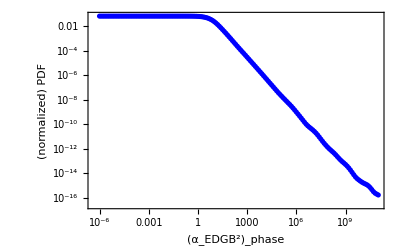

```mathematica
plotαFinalPDFPhaseLogNorm=ListLogLogPlot[{αFinalPDFPhaseLogNorm},PlotRange->All,PlotRange->All,Frame->True,PlotStyle->{Blue,Red},FrameLabel->{"(α_EDGB^2)_phase","(normalized) PDF"}]
```

```mathematica
αFinalPDFPhaseInterpLogNorm=Interpolation[αFinalPDFPhaseLogNorm];
```

```mathematica
αFinalCDFPhaseNorm=Table[{αSampleLog[[i]],NIntegrate[αFinalPDFPhaseInterpLogNorm[x],{x,0,αSampleLog[[i]]}]},{i,1,Length[αSampleLog]}];
```

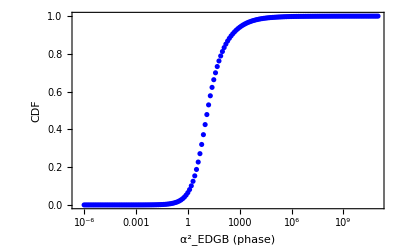

```mathematica
ListLogLinearPlot[αFinalCDFPhaseNorm,PlotRange->All,PlotRange->All,Frame->True,PlotStyle->{Blue},FrameLabel->{"α^2_EDGB (phase)","CDF"}]
```

```mathematica
αFinalCDFPhaseNormInterp=Interpolation[αFinalCDFPhaseNorm];
```

```mathematica
αSquared90CLphase=x/.FindRoot[αFinalCDFPhaseNormInterp[x]==0.9,{x,100}] (*90% CL of Subscript[α^2, EDGB] from phase correction *)
```

347.918

```mathematica
√√αSquared90CLphase//N
```

4.31886

```mathematica
4.720526510106356
```

4.72053

```mathematica
Subscript[α^2, EDGB] from amplitude correction:
```

```mathematica
LogSquaredαamp=Log[SqrtαEDGBamp^4]
```

{6.07248,10.1381,6.76496,7.90959,9.82486,6.66321,5.63673,7.28702,52236,5.97281,6.2432,6.19856,3.64171,6.51077,9.45411,6.43167,7.17605}
 |  |  |  |

```mathematica
Max[LogSquaredαamp]
```

29.2372

```mathematica
Min[LogSquaredαamp]
```

2.30312

```mathematica
𝒟logαamp=HistogramDistribution[LogSquaredαamp] ;
```

```mathematica
pslogαamp=PDF[𝒟logαamp,x];
```

```mathematica
Histogram[LogSquaredαamp];
```

```mathematica
αampMC[x_]=pslogαamp;
```

```mathematica
αampMC[2.25]
```

0.000229656

```mathematica
αampMC[30]
```

0.

```mathematica
αMCSampleamp=Range[2.25,30,0.5];
```

```mathematica
αMCTableamp=Table[{αMCSampleamp[[i]],αampMC[αMCSampleamp[[i]]]},{i,1,Length[αMCSampleamp]}];
```

```mathematica
αMCTableInterpamp=Interpolation[αMCTableamp];
```

```mathematica
plotαMCTableInterpamp=Plot[αMCTableInterpamp[x],{x,2.25,30},PlotStyle->Blue,PlotLegends->{"Interpolation"},PlotRange->All];
```

```mathematica
plot6=Plot[αampMC[x],{x,2,30},Filling->Axis,PlotStyle->Gray,PlotRange->All];
```

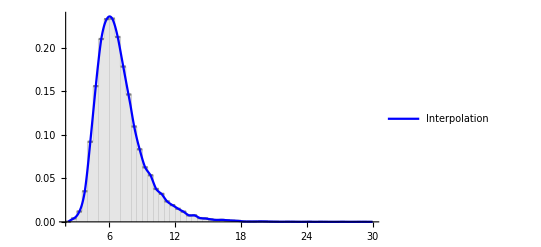

```mathematica
Show[plot6,plotαMCTableInterpamp]
```

```mathematica
αSampleLogamp=Prepend[10^Range[-6,11,0.1],0];
```

```mathematica
fun1αamp[x_,y_]=1/(√(2*π)*Exp[y])*Exp[-x^2/(2Exp[2*y])];
```

```mathematica
fun1αampTable[y_]=Table[{αSampleLogamp[[i]],fun1αphase[αSampleLogamp[[i]],y]},{i,1,Length[αSampleLogamp]}];
```

```mathematica
αFinalPDFampLog=Table[{fun1αampTable[y][[i,1]],NIntegrate[fun1αampTable[y][[i,2]]αMCTableInterpamp[y],{y,2.25,30}]},{i,1,Length[fun1αampTable[y]]}];
```

```mathematica
αFinalPDFampInterpLog=Interpolation[αFinalPDFampLog]
```

InterpolatingFunction[…]

```mathematica
αNormalizationamp=NIntegrate[αFinalPDFampInterpLog[x],{x,0,10^11}]
```

0.499555

```mathematica
αFinalPDFampLogNorm=Table[{αFinalPDFampLog[[i,1]],αFinalPDFampLog[[i,2]]/αNormalizationamp},{i,1,Length[αFinalPDFampLog]}];
```

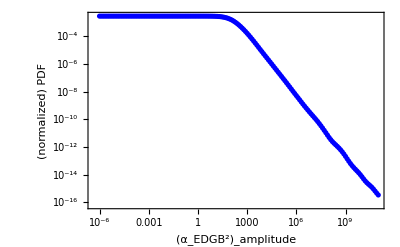

```mathematica
plotαFinalPDFampLogNorm=ListLogLogPlot[{αFinalPDFampLogNorm},PlotRange->All,PlotRange->All,Frame->True,PlotStyle->{Blue,Red},FrameLabel->{"(α_EDGB^2)_amplitude","(normalized) PDF"}]
```

```mathematica
αFinalPDFampInterpLogNorm=Interpolation[αFinalPDFampLogNorm];
```

```mathematica
αFinalCDFampNorm=Table[{αSampleLogamp[[i]],NIntegrate[αFinalPDFampInterpLogNorm[x],{x,0,αSampleLogamp[[i]]}]},{i,1,Length[αSampleLogamp]}];
```

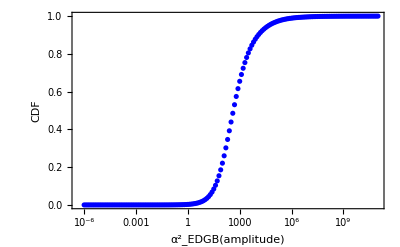

```mathematica
ListLogLinearPlot[αFinalCDFampNorm,PlotRange->All,PlotRange->All,Frame->True,PlotStyle->{Blue},FrameLabel->{"α^2_EDGB(amplitude)","CDF"}]
```

```mathematica
αFinalCDFampNormInterp=Interpolation[αFinalCDFampNorm];
```

```mathematica
αSquared90CLamp=x/.FindRoot[αFinalCDFampNormInterp[x]==0.9,{x,1000}](*90% CL of Subscript[α^2, EDGB] from phase correction *)
```

11881.

```mathematica
√√αSquared90CLamp
```

10.4403

```mathematica
11.405946092337743
```

11.4059

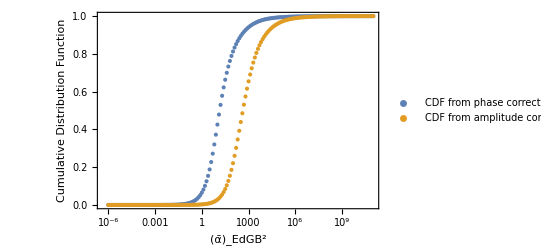

```mathematica
PlotCDFComparison=ListLogLinearPlot[{αFinalCDFPhaseNorm,αFinalCDFampNorm},PlotRange->All,TicksStyle->Directive["Label",14],AxesLabel->{nPN,Subscript[σ, α]},PlotLegends->{Placed[LineLegend[{"CDF from phase correction  ","CDF from amplitude correction"},LabelStyle->{FontSize->5},LegendMarkerSize->10,LegendMargins->0,LegendFunction->"Frame"],{Left,Top}]},FrameLabel->{"(ᾱ)_EdGB^2","Cumulative Distribution Function"},Frame->True]
```

## ζ from phase correction

### 2D Gaussian, ζ samples

```mathematica
𝒟log=HistogramDistribution[Log[ζphaseAll]] (*simga_zeta from log of phase correction from monte-carlo. If we use the distribution of ζ, the pdf we get looks almost rectangular. That is why we are using the log[sigma_zeta]. We can compare their shapes from following two histograms *)
```

DataDistribution[…]

```mathematica
Histogram[Log[ζphaseAll]];
```

```mathematica
Histogram[ζphaseAll];
```

```mathematica
ps1=PDF[𝒟log,x];
```

```mathematica
ps2[x]=ps1;
```

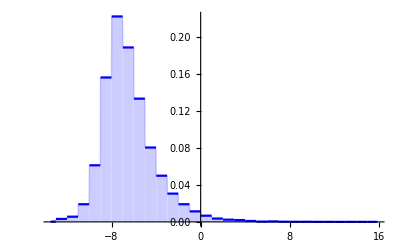

```mathematica
plottest2=Plot[ps2[x],{x,Log[Min[ζphaseAll]],Log[Max[ζphaseAll]]},Filling->Axis,PlotStyle->Blue,PlotRange->All]
```

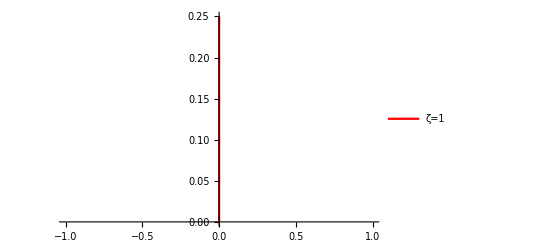

```mathematica
zeta1=ListLinePlot[{{0,0},{0,0.25}},PlotStyle->Red,PlotLegends->{Placed[LineLegend[{"ζ=1"},LabelStyle->{Orange,FontSize->10},LegendMarkerSize->8,LegendMargins->0,LegendFunction->"Frame"],{Right,Top}]}]
```

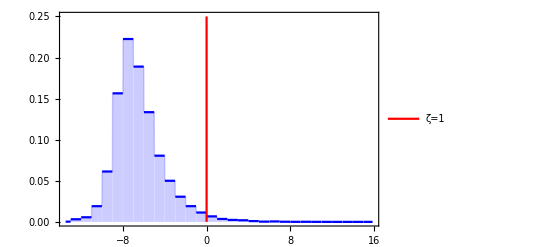

```mathematica
Show[plottest2,zeta1,Frame->True,PlotRange->All] (*Shows how much of the area under the curve satisfies zeta<1 from phase correction*)
```

```mathematica
Integrate[ps2[x],{x,Log[Min[ζphaseAll]],Log[Max[ζphaseAll]]}]
```

0.999836

```mathematica
Integrate[ps2[x],{x,-Infinity,Infinity}]
```

1.

```mathematica
Integrate[ps2[x],{x,Log[Min[ζphaseAll]],0}]/Integrate[ps2[x],{x,Log[Min[ζphaseAll]],Log[Max[ζphaseAll]]}]*100 (*98% area under the curve satisfies zeta<1 from phase correction*)
```

98.2835

```mathematica
MaxLogζphase=Log[Max[ζphaseAll]]
```

15.8769

```mathematica
MinLogζphase=Log[Min[ζphaseAll]]
```

-13.4813

```mathematica
fun1kent[x_,y_]=1/(√(2*π) Exp[y])*Exp[-x^2/(2Exp[2y])]
```

(ⅇ^(-1/2 ⅇ^(-2 y) x^2-y))/(√(2 π))

ζ sample

```mathematica
ζSampleLog=Prepend[10^Range[-5,3,0.1],0];
```

Creating a table for fun1Kent[x,y] at each ζ sample for x

```mathematica
fun1TableLog[y_]=Table[{ζSampleLog[[i]],fun1kent[ζSampleLog[[i]],y]},{i,1,Length[ζSampleLog]}];
```

```mathematica
ζMC[x_]=ps1;
```

```mathematica
ζMC[-14.5]
ζMC[16.5]
```

0.

0.

ζ sample for creating an interpolation function for the MC prob distribution
Since ζ > 0, I only consider positive ζ

```mathematica
ζMCSample=Range[-14.5,16.5,1];
```

creating a table for the MC distribution at each sample ζ

```mathematica
ζMCTable=Table[{ζMCSample[[i]],ζMC[ζMCSample[[i]]]},{i,1,Length[ζMCSample]}];
```

creating an interpolation function

```mathematica
ζMCTableInterp=Interpolation[ζMCTable];
```

Plot

```mathematica
plotζMCTableInterp=Plot[ζMCTableInterp[x],{x,-14.5,16.5},PlotStyle->Blue,PlotLegends->{"Interpolation"}];
```

Comparison with the actual distribution

```mathematica
Show[plotζMCTableInterp,plottest2,Frame->True,FrameLabel->{"Log σ_ζ","PDF"}];
```

```mathematica
ζFinalPDFPhaseLog=Table[{fun1TableLog[y][[i,1]],NIntegrate[fun1TableLog[y][[i,2]]ζMCTableInterp[y],{y,MinLogζphase,MaxLogζphase}]},{i,1,Length[fun1TableLog[y]]}];
```

#### Normalized Distribution

Interpolation

```mathematica
ζFinalPDFPhaseInterpLog=Interpolation[ζFinalPDFPhaseLog];
```

Normalization

```mathematica
Normalization=NIntegrate[ζFinalPDFPhaseInterpLog[x],{x,0,1000}]
```

0.498985

Normalized distribution

```mathematica
ζFinalPDFPhaseLogNorm=Table[{ζFinalPDFPhaseLog[[i,1]],ζFinalPDFPhaseLog[[i,2]]/Normalization},{i,1,Length[ζFinalPDFPhaseLog]}];
```

Plot

```mathematica
plotζFinalPDFPhaseLogNorm=ListLogLogPlot[{ζFinalPDFPhaseLogNorm},PlotRange->All,PlotRange->All,Frame->True,PlotStyle->{Blue,Red},FrameLabel->{"ζ","(normalized) PDF"}];
```

#### Cumulative Distribution

Interpolation

```mathematica
ζFinalPDFPhaseInterpLogNorm=Interpolation[ζFinalPDFPhaseLogNorm];
```

Creating a table for cumulative distribution

```mathematica
ζFinalCDFPhaseNorm=Table[{ζSampleLog[[i]],NIntegrate[ζFinalPDFPhaseInterpLogNorm[x],{x,0,ζSampleLog[[i]]}]},{i,1,Length[ζSampleLog]}];
```

Plot

```mathematica
ListLogLinearPlot[ζFinalCDFPhaseNorm,PlotRange->All,PlotRange->All,Frame->True,PlotStyle->{Blue},FrameLabel->{"ζ","CDF"}];
```

CDF nicely asymptotes to 1 (suggesting that ζ = 100 is large enough)

#### Finding 90% credible limit for ζ

Interpolation for CDF

```mathematica
ζFinalCDFPhaseNormInterp=Interpolation[ζFinalCDFPhaseNorm];
```

90% limit

```mathematica
ζ90CLphase=x/.FindRoot[ζFinalCDFPhaseNormInterp[x]==0.9,{x,0.02}]
```

0.0205204

```mathematica
ζ  from amplitude correction
```

amplitude correction from ζ

```mathematica
𝒟logamp=HistogramDistribution[Log[ζampAll]] (*zeta from log of amp correction from monte-carlo*)
```

DataDistribution[…]

```mathematica
Histogram[Log[ζampAll]];
```

```mathematica
Histogram[ζampAll];
```

```mathematica
ps1amp=PDF[𝒟logamp,x];
ps2amp[x]=ps1amp;
```

```mathematica
MinLogζamp=Min[Log[ζampAll]]
```

-10.7176

```mathematica
MaxLogζamp=Max[Log[ζampAll]]
```

19.4335

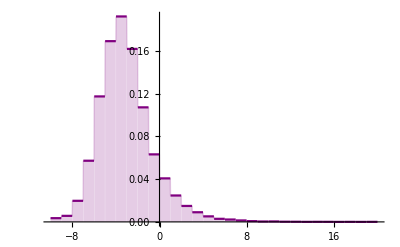

```mathematica
plottestamp=Plot[ps2amp[x],{x,-10,20},Filling->Axis,PlotStyle->Purple]
```

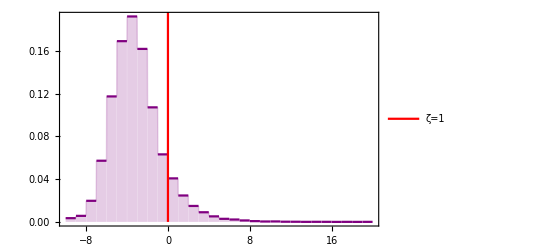

```mathematica
Show[plottestamp,zeta1,Frame->True] (*Shows how much of the area under the curve satisfies zeta<1 from amplitude correction*)
```

```mathematica
Integrate[ps2amp[x],{x,Log[Min[ζampAll]],Log[Max[ζampAll]]}]
```

0.9998

```mathematica
Integrate[ps2amp[x],{x,Log[Min[ζampAll]],0}]/Integrate[ps2amp[x],{x,Log[Min[ζampAll]],Log[Max[ζampAll]]}]*100 (*89.7% area under the curve satisfies zeta<1 from amplitude correction*)
```

89.7039

```mathematica
ζSampleLogamp=Prepend[10^Range[-5,3,0.1],0];
```

```mathematica
fun1TableLogamp[y_]=Table[{ζSampleLogamp[[i]],fun1kent[ζSampleLogamp[[i]],y]},{i,1,Length[ζSampleLogamp]}];
```

```mathematica
ζMCamp[x_]=ps1amp;
```

```mathematica
ζMCamp[-11.5]
ζMCamp[20]
```

0.

0.

```mathematica
ζMCSampleamp=Range[-11.5,20,1];
```

```mathematica
ζMCTableamp=Table[{ζMCSampleamp[[i]],ζMCamp[ζMCSampleamp[[i]]]},{i,1,Length[ζMCSampleamp]}];
```

```mathematica
ζMCTableInterpamp=Interpolation[ζMCTableamp];
```

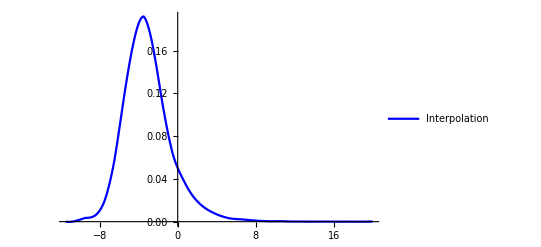

```mathematica
plotζMCTableInterpamp=Plot[ζMCTableInterpamp[x],{x,-11.5,20},PlotStyle->Blue,PlotLegends->{"Interpolation"}]
```

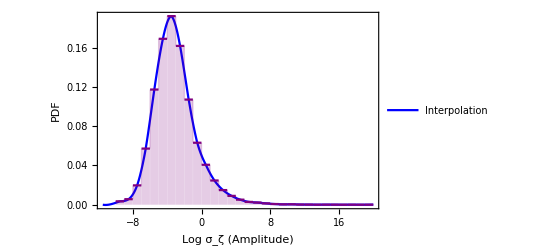

```mathematica
Show[plotζMCTableInterpamp,plottestamp,Frame->True,FrameLabel->{"Log σ_ζ (Amplitude)","PDF"}]
```

```mathematica
ζFinalPDFampLog=Table[{fun1TableLogamp[y][[i,1]],NIntegrate[fun1TableLogamp[y][[i,2]]ζMCTableInterpamp[y],{y,MinLogζamp,MaxLogζamp}]},{i,1,Length[fun1TableLogamp[y]]}];
```

```mathematica
ζFinalPDFampInterpLog=Interpolation[ζFinalPDFampLog];
```

Normalization

```mathematica
Normalizationζamp=NIntegrate[ζFinalPDFampInterpLog[x],{x,0,1000}]
```

0.497949

```mathematica
ζFinalPDFampLogNorm=Table[{ζFinalPDFampLog[[i,1]],ζFinalPDFampLog[[i,2]]/Normalizationζamp},{i,1,Length[ζFinalPDFampLog]}];
```

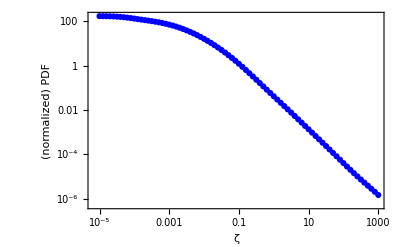

```mathematica
plotζFinalPDFampLogNorm=ListLogLogPlot[{ζFinalPDFampLogNorm},PlotRange->All,PlotRange->All,Frame->True,PlotStyle->{Blue,Red},FrameLabel->{"ζ","(normalized) PDF"}]
```

```mathematica
ζFinalPDFampInterpLogNorm=Interpolation[ζFinalPDFampLogNorm];
```

```mathematica
ζFinalCDFampNorm=Table[{ζSampleLogamp[[i]],NIntegrate[ζFinalPDFampInterpLogNorm[x],{x,0,ζSampleLogamp[[i]]}]},{i,1,Length[ζSampleLogamp]}];
```

```mathematica
ListLogLinearPlot[ζFinalCDFampNorm,PlotRange->All,PlotRange->All,Frame->True,PlotStyle->{Blue},FrameLabel->{"ζ","CDF"}];
```

```mathematica
ζFinalCDFampNormInterp=Interpolation[ζFinalCDFampNorm];
```

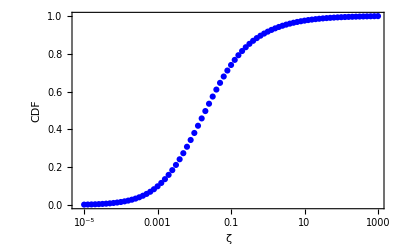

```mathematica
ListLogLinearPlot[ζFinalCDFampNorm,PlotRange->All,PlotRange->All,Frame->True,PlotStyle->{Blue},FrameLabel->{"ζ","CDF"}]
```

```mathematica
ζ90CLamp=x/.FindRoot[ζFinalCDFampNormInterp[x]==0.9,{x,0.02}]
```

0.676947

```mathematica
Combining the upper bounds on ζ from phase and amplitude corrections:
```

```mathematica
ζphaseAll
```

{0.000527219,0.04629,0.00149139,0.00472299,0.0315425,0.00108356,0.000412873,52238,0.000633543,0.000802919,0.0000271997,0.00113999,0.020969,0.000912693,0.00193851}
 |  |  |  |

```mathematica
ζampAll
```

{0.0171763,1.58619,0.0522075,0.165549,1.09246,0.0378357,0.0127864,52238,0.0140803,0.0231292,0.000514475,0.0374042,0.727602,0.0315771,0.0686092}
 |  |  |  |

```mathematica
ζcombined=(1/ζphaseAll^2+1/ζphaseAll^2)^(-1/2)
```

{0.0003728,0.032732,0.00105457,0.00333966,0.0223039,0.000766195,0.000291945,52238,0.000447983,0.000567749,0.0000192331,0.000806096,0.0148273,0.000645371,0.00137073}
 |  |  |  |

```mathematica
𝒟logζcomb=HistogramDistribution[Log[ζcombined]]
```

DataDistribution[…]

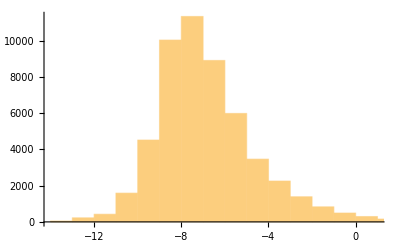

```mathematica
Histogram[Log[ζcombined]]
```

```mathematica
MinLogζcomb=Min[Log[ζcombined]]
```

-13.8279

```mathematica
MaxLogζcomb=Max[Log[ζcombined]]
```

15.5303

```mathematica
ps1ζcomb=PDF[𝒟logζcomb,x];
ps2ζcomb[x]=ps1ζcomb;
```

```mathematica
plotζcomb=Plot[ps2ζcomb[x],{x,-13,16},Filling->Axis,PlotStyle->Gray];
```

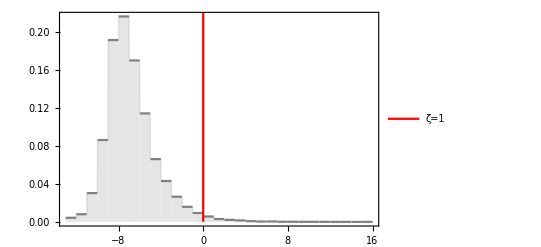

```mathematica
Show[plotζcomb,zeta1,Frame->True] (*Shows how much of the area under the curve satisfies zeta<1 from the combination of phase and amplitude*)
```

```mathematica
Integrate[ps2ζcomb[x],{x,MinLogζcomb,MaxLogζcomb}]
```

0.999817

```mathematica
Integrate[ps2ζcomb[x],{x,MinLogζcomb,0}]/Integrate[ps2ζcomb[x],{x,MinLogζcomb,MaxLogζcomb}]*100 (*89.7% area under the curve satisfies zeta<1 from amplitude correction*)
```

98.5413

```mathematica
ζSampleLogcomb=Prepend[10^Range[-5,3,0.1],0];
```

```mathematica
fun1TableLogcomb[y_]=Table[{ζSampleLogcomb[[i]],fun1kent[ζSampleLogamp[[i]],y]},{i,1,Length[ζSampleLogcomb]}];
```

```mathematica
ζMCcomb[x_]=ps1ζcomb;
```

```mathematica
ζMCcomb[-14.5]
ζMCcomb[20]
```

0.

0.

```mathematica
ζMCSamplecomb=Range[-14.5,20,1];
```

```mathematica
ζMCTablecomb=Table[{ζMCSamplecomb[[i]],ζMCcomb[ζMCSamplecomb[[i]]]},{i,1,Length[ζMCSamplecomb]}];
```

```mathematica
ζMCTableInterpcomb=Interpolation[ζMCTablecomb];
```

InterpolatingFunction::dmval: Input value {-14.9993} lies outside the range of data in the interpolating function. Extrapolation will be used.

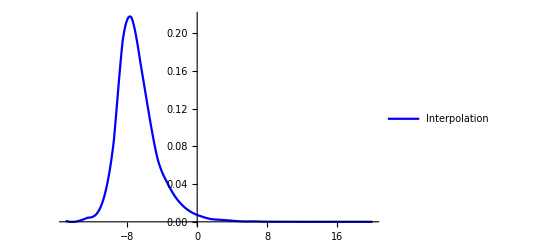

```mathematica
plotζMCTableInterpcomb=Plot[ζMCTableInterpcomb[x],{x,-15,20},PlotStyle->Blue,PlotLegends->{"Interpolation"},PlotRange->All]
```

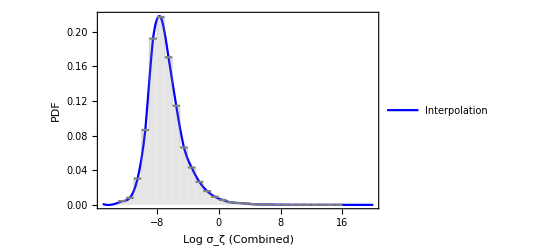

```mathematica
Show[plotζMCTableInterpcomb,plotζcomb,Frame->True,FrameLabel->{"Log σ_ζ (Combined)","PDF"}]
```

```mathematica
ζFinalPDFcombLog=Table[{fun1TableLogcomb[y][[i,1]],NIntegrate[fun1TableLogcomb[y][[i,2]]ζMCTableInterpcomb[y],{y,MinLogζcomb,MaxLogζcomb}]},{i,1,Length[fun1TableLogcomb[y]]}];
```

```mathematica
ζFinalPDFcombInterpLog=Interpolation[ζFinalPDFcombLog];
```

Normalization

```mathematica
Normalizationζcomb=NIntegrate[ζFinalPDFcombInterpLog[x],{x,0,1000}]
```

0.499071

```mathematica
ζFinalPDFcombLogNorm=Table[{ζFinalPDFcombLog[[i,1]],ζFinalPDFcombLog[[i,2]]/Normalizationζcomb},{i,1,Length[ζFinalPDFcombLog]}];
```

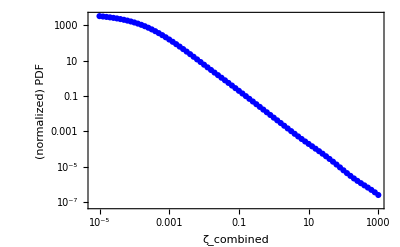

```mathematica
plotζFinalPDFcombLogNorm=ListLogLogPlot[{ζFinalPDFcombLogNorm},PlotRange->All,PlotRange->All,Frame->True,PlotStyle->{Blue,Red},FrameLabel->{"ζ_combined","(normalized) PDF"}]
```

```mathematica
ζFinalPDFcombInterpLogNorm=Interpolation[ζFinalPDFcombLogNorm]
```

InterpolatingFunction[…]

```mathematica
ζFinalCDFcombNorm=Table[{ζSampleLogcomb[[i]],NIntegrate[ζFinalPDFcombInterpLogNorm[x],{x,0,ζSampleLogcomb[[i]]}]},{i,1,Length[ζSampleLogcomb]}];
```

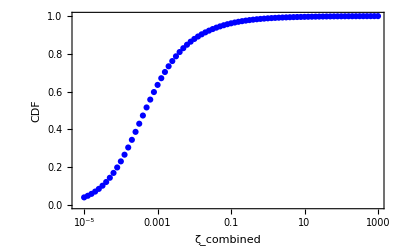

```mathematica
ListLogLinearPlot[ζFinalCDFcombNorm,PlotRange->All,PlotRange->All,Frame->True,PlotStyle->{Blue},FrameLabel->{"ζ_combined","CDF"}]
```

```mathematica
ζFinalCDFcombNormInterp=Interpolation[ζFinalCDFcombNorm];
```

```mathematica
ζ90CLcomb=x/.FindRoot[ζFinalCDFcombNormInterp[x]==0.9,{x,0.02}]
```

0.0146834

```mathematica
Combining the upper bounds of Subscript[α^2, EDGB] from phase and amplitude corrections:
```

```mathematica
SquaredαEDGBcomb=(1/((SqrtαEDGBphase^4)^2)+1/((SqrtαEDGBamp^4)^2))^(-1/2)
```

{13.3077,737.692,24.7551,77.6613,533.572,22.4166,9.05409,54.2208,52236,11.8754,23.1266,17.0706,2.0145,20.482,367.598,17.9478,36.9342}
 |  |  |  |

```mathematica
SqrtαEDGBphase^4
```

{13.3139,738.006,24.7652,77.6929,533.795,22.4258,9.05881,54.2582,52236,11.8808,23.15,17.0809,2.01731,20.4915,367.75,17.9553,36.9489}
 |  |  |  |

```mathematica
LogSquaredαcomb=Log[SquaredαEDGBcomb] (*This is Log of sigma_(alpha^2)*)
```

{2.58834,6.60353,3.20903,4.35236,6.27959,3.1098,2.20322,3.99306,52236,2.47447,3.14098,2.83736,0.700369,3.01955,5.90699,2.88747,3.60914}
 |  |  |  |

```mathematica
Max[LogSquaredαcomb]
```

25.6801

```mathematica
Min[LogSquaredαcomb]
```

-0.47644

```mathematica
𝒟logαcomb=HistogramDistribution[LogSquaredαcomb] ;
```

```mathematica
pslogαcomb=PDF[𝒟logαcomb,x];
```

```mathematica
Histogram[LogSquaredαcomb];
```

```mathematica
fun1αcomb[x_,y_]=1/(√(2*π)*Exp[y])*Exp[-x^2/(2Exp[2*y])] (*P(α^2|Subscript[σ, α^2])*)
```

(ⅇ^(-1/2 ⅇ^(-2 y) x^2-y))/(√(2 π))

```mathematica
αSampleLog=Prepend[10^Range[-6,11,0.1],0];
```

```mathematica
αcombMC[x_]=pslogαcomb;
```

```mathematica
αcombMC[-0.5]
```

0.00218173

```mathematica
αcombMC[26.5]
```

0.

```mathematica
αMCSamplecomb=Range[-0.25,26.5,0.5];
```

```mathematica
αMCTablecomb=Table[{αMCSamplecomb[[i]],αcombMC[αMCSamplecomb[[i]]]},{i,1,Length[αMCSamplecomb]}];
```

```mathematica
αMCTableInterpcomb=Interpolation[αMCTablecomb];
```

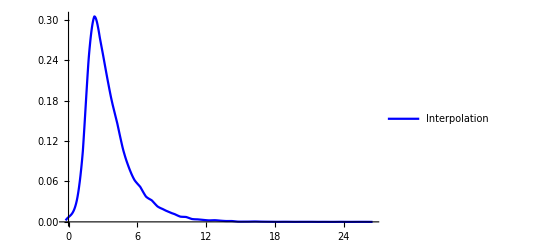

```mathematica
plotαMCTableInterpcomb=Plot[αMCTableInterpcomb[x],{x,-0.25,26.5},PlotStyle->Blue,PlotLegends->{"Interpolation"},PlotRange->All]
```

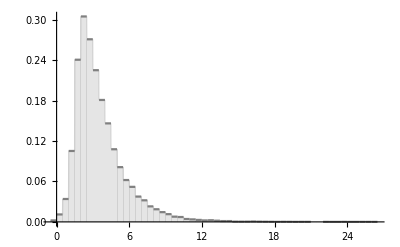

```mathematica
plot8=Plot[αcombMC[x],{x,-0.5,26.5},Filling->Axis,PlotStyle->Gray,PlotRange->All]
```

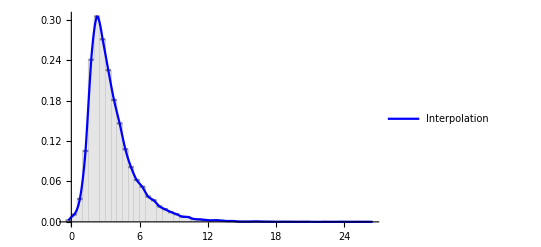

```mathematica
Show[plot8,plotαMCTableInterpcomb] (*Interpolation matches the actual pdf of monte-carlo*)
```

```mathematica
fun1αcombTable[y_]=Table[{αSampleLog[[i]],fun1αcomb[αSampleLog[[i]],y]},{i,1,Length[αSampleLog]}];
```

```mathematica
αFinalPDFcombLog=Table[{fun1αcombTable[y][[i,1]],NIntegrate[fun1αcombTable[y][[i,2]]αMCTableInterpcomb[y],{y,-0.25,26.5}]},{i,1,Length[fun1αcombTable[y]]}];
```

```mathematica
αFinalPDFcombInterpLog=Interpolation[αFinalPDFcombLog]
```

InterpolatingFunction[…]

```mathematica
αNormalizationcomb=NIntegrate[αFinalPDFcombInterpLog[x],{x,0,10^11}]
```

0.499591

```mathematica
αFinalPDFcombLogNorm=Table[{αFinalPDFcombLog[[i,1]],αFinalPDFcombLog[[i,2]]/αNormalizationcomb},{i,1,Length[αFinalPDFcombLog]}];
```

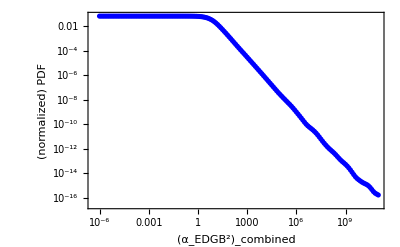

```mathematica
plotαFinalPDFcombLogNorm=ListLogLogPlot[{αFinalPDFcombLogNorm},PlotRange->All,PlotRange->All,Frame->True,PlotStyle->{Blue,Red},FrameLabel->{"(α_EDGB^2)_combined","(normalized) PDF"}]
```

```mathematica
αFinalPDFcombInterpLogNorm=Interpolation[αFinalPDFcombLogNorm]
```

InterpolatingFunction[…]

```mathematica
αFinalCDFcombNorm=Table[{αSampleLog[[i]],NIntegrate[αFinalPDFcombInterpLogNorm[x],{x,0,αSampleLog[[i]]}]},{i,1,Length[αSampleLog]}];
```

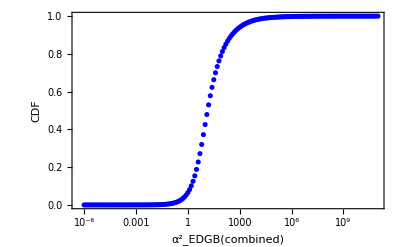

```mathematica
ListLogLinearPlot[αFinalCDFcombNorm,PlotRange->All,PlotRange->All,Frame->True,PlotStyle->{Blue},FrameLabel->{"α^2_EDGB(combined)","CDF"}]
```

```mathematica
αFinalCDFcombNormInterp=Interpolation[αFinalCDFcombNorm];
```

```mathematica
αSquared90CLcomb=x/.FindRoot[αFinalCDFcombNormInterp[x]==0.9,{x,100}](*90% CL of Subscript[α^2, EDGB] from phase correction *)
```

347.8

```mathematica
√√αSquared90CLcomb
```

4.31849

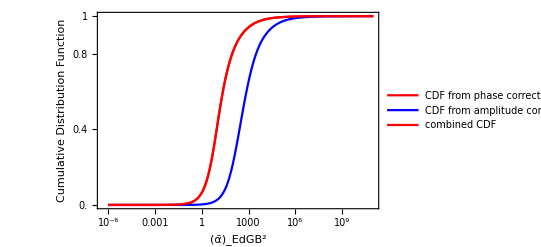

```mathematica
PlotCDFComparisonAll=ListLogLinearPlot[{αFinalCDFPhaseNorm,αFinalCDFampNorm,αFinalCDFcombNorm},Joined->True,PlotRange->All,PlotStyle->{Red,Blue},PlotLegends->{Placed[LineLegend[{"CDF from phase correction  ","CDF from amplitude correction","combined CDF"},LabelStyle->{Orange,FontSize->5},LegendMarkerSize->8,LegendMargins->0,LegendFunction->"Frame"],{Right,Bottom}]},FrameLabel->{"(ᾱ)_EdGB^2","Cumulative Distribution Function"},FrameStyle->Directive[Gray,Dashed],Frame->True,FrameTicks->{Automatic,{0.0,0.2,0.4,0.6,0.8,0.9,1}},FrameTicksStyle->Directive[Black,9]]
```

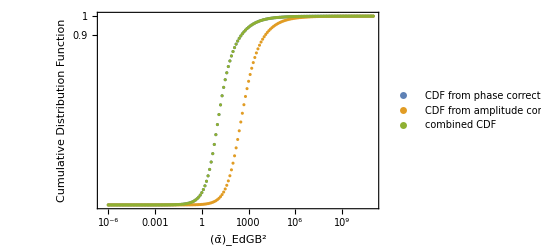

```mathematica
ListLogLinearPlot[{αFinalCDFPhaseNorm,αFinalCDFampNorm,αFinalCDFcombNorm},PlotRange->All,PlotLegends->{Placed[LineLegend[{"CDF from phase correction  ","CDF from amplitude correction","combined CDF"},LabelStyle->{Red,FontSize->5},LegendMarkerSize->5,LegendMargins->0,LegendFunction->"Frame"],{Left,Top}]},FrameLabel->{"(ᾱ)_EdGB^2","Cumulative Distribution Function"},Frame->True, FrameTicks->{{0,19},{0.9,1}}]
```

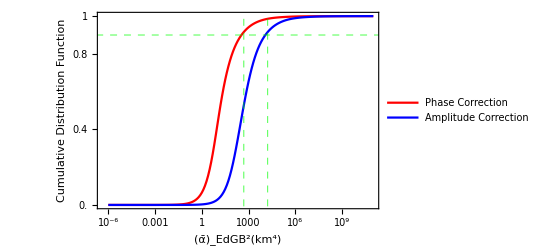

```mathematica
GraphExport=ListLogLinearPlot[{αFinalCDFPhaseNorm,αFinalCDFampNorm},Joined->True,PlotRange->All,PlotStyle->{Red,Blue},GridLines->{{496.714,16966.493133860196},{0.9}},GridLinesStyle->Directive[Green, Dashed],PlotLegends->{Placed[LineLegend[{"Phase Correction  ","Amplitude Correction"},LabelStyle->{Orange,FontSize->10},LegendMarkerSize->8,LegendMargins->0,LegendFunction->"Frame"],{Right,Bottom}]},Frame->True,FrameLabel->{Style["(ᾱ)_EdGB^2(km^4)",14],Style["Cumulative Distribution Function",12]},LabelStyle->{Purple,FontSize->10},FrameTicks->{{#,ScientificForm@#}&/@{0.00001,0.01,347.9,11881,10000000.0},{0.0,0.2,0.4,0.6,0.8,0.9,1}}]
```

```mathematica
Export[NotebookDirectory[]<>"EdGBGW151226.pdf",GraphExport,ImageResolution->2000]
```

/Users/stshammi/temp/EDGB_bound/GW151226/EdGBGW151226.pdf

```mathematica
"/Users/stshammi/temp/EDGB_bound/GW151226/EdGB-GW151226.pdf"
```

/Users/stshammi/temp/EDGB_bound/GW151226/EdGB-GW151226.pdf

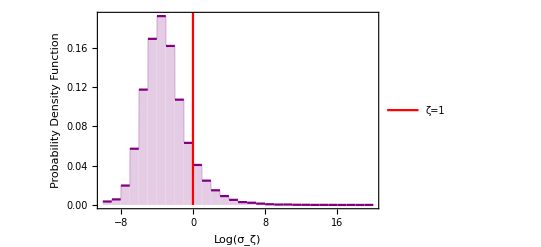

```mathematica
GraphExport3=Show[plottestamp,zeta1,Frame->True,FrameLabel->{Style["Log(σ_ζ)",FontSize->15],Style["Probability Density Function",FontSize->15]},LabelStyle->Purple]
```

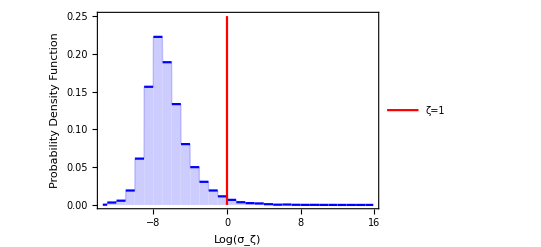

```mathematica
GraphExport2=Show[plottest2,zeta1,Frame->True,FrameLabel->{Style["Log(σ_ζ)",
FontSize->15],Style["Probability Density Function",FontSize->15]},LabelStyle->Purple]
```

```mathematica
Export[NotebookDirectory[]<>"pdf1.pdf",GraphExport2,ImageResolution->2000]
```

/Users/stshammi/temp/EDGB_bound/GW151226/pdf1.pdf

```mathematica
Export[NotebookDirectory[]<>"pdf2.pdf",GraphExport3,ImageResolution->2000]
```

/Users/stshammi/temp/EDGB_bound/GW151226/pdf2.pdf